Blocks Problem: Ricostruire la parola "universal" attraverso un algoritmo genetico. (Koza)

Dati

```mathematica
(******************************************************************************************************************************************************)(*SCRIVO I DATI DEL PROBLEMA. ANDRÒ QUINDI A DEFINIRE I VETTORI STACK E TABLE E IL NUMERO DI INDIVIDUI CHE COSTITUISCONO LA POPOLAZIONE*)
(******************************************************************************************************************************************************)
uni={u,n,i,v,e,r,s,a,l};
uniR=RandomSample[uni];
taglio=RandomInteger[{0,9}];
cut=taglio;
stack0=Take[uniR,cut];
table0=Take[uniR,-(9-cut)];
pop=50;
```

Funzioni

```mathematica
(******************************************************************************************************************************************************)(*SE LA LUNGHEZZA DI STACK È DIVERSA DA 0. ALLORA ESTRAGGO IL PRIMO ELEMNTO DI STACK. IN TERMINI GRAFICI ESTRAGGO L'ELEMENTO IN ALTO DELLA PILA*)
(******************************************************************************************************************************************************)
CS:=Module[{temp},
If[Length[stack]==0,
NIL,
stack[[1]]
]
]
(******************************************************************************************************************************************************)(*VALUTO STACK PARTENDO DAL FONDO; SE È IN PARTE CORRETTO, IL PROGRAMMA RESTITUISCE L'ULTIMA LETTERA CORRETTA DI STACK*)
(******************************************************************************************************************************************************)
TB:=Module[{i,l},
If[stack===uni,
Return[NIL]
];

If[Length[stack]===0,
NIL,
If[stack[[-1]]===uni[[9]],
For[i=0,i≤Length[stack]+1,i++,
If[stack[[Length[stack]-i]]===uni[[9-i]],
True,
Return[uni[[9-i+1]]]
]
],
NIL
]
]
]
(******************************************************************************************************************************************************)(*SE STACK È UN BLOCCO DI LETTERE CORRETTE, RESTITUISCE LA PROSSIMA LETTERA NECESSARIA*)
(******************************************************************************************************************************************************)
NN:=If[Length[stack]===0,
Return[l],
If[Length[stack]===9,
Return[NIL],
If[stack[[1]]===TB,
Return[uni[[9-Length[stack]]]],
Return[NIL]
]
]
]
(******************************************************************************************************************************************************)(*SE L'ELEMNENTO x SI TROVA IN TABLE LO SPOSTO IN CIMA A STACK E QUINDI AL PRIMO POSTO DI STACK*)
(******************************************************************************************************************************************************)
MS[x_]:=If[MemberQ[table,x]===True,
stack=Prepend[stack,x];
table=DeleteCases[table,x];
x,
NIL
]
(******************************************************************************************************************************************************)(*SE L'ELEMENTO x SI TROVA IN STACK SPOSTO IL PRIMO ELEMENTO DI STACK AL PRIMO POSTO DI TABLE*)
(******************************************************************************************************************************************************)
MT[x_]:=If[MemberQ[stack,x]===True,
table=Prepend[table,stack[[1]]];
stack=DeleteCases[stack,stack[[1]]];
x,
NIL
]
(******************************************************************************************************************************************************)(*VALUTO PER UN MASSIMO DI 30 VOLTE x1 FICNHÈ x2 DIVENTA VERO. SE NON RIESCO IN 30 TENTATIVI RESTITUISCO "TRUE"*)
(******************************************************************************************************************************************************)
DU[exp1_,exp2_]:=Module[{temp,i},
For[i=0,i≤10,i++,
If[exp2===NIL,exp1,Return[TRUE]];
If[i===10,Return[NIL]]]
]
SetAttributes[DU,HoldAll]
(******************************************************************************************************************************************************)(*VALUTO x1. SE È NULLO RESTITUISCE "TRUE" ALTRIMENTI "FALSE"*)
(******************************************************************************************************************************************************)
NOT[exp1_]:=If[exp1===NIL,TRUE,NIL]
(******************************************************************************************************************************************************)(*VALUTO x1 E x2, SE SONO UGUALI RESTITUISCE "TRUE", ALTRIMENTI "FALSE"*)
(******************************************************************************************************************************************************)
EQ[exp1_,exp2_]:=If[exp1===exp2,TRUE,NIL]
```

Divisione Funzioni

```mathematica
(******************************************************************************************************************************************************)(*DIVIDO IN SOTTO GRUPPI LE FUNZIONI APPENA DEFINITE IN FUNZIONE DEL LORO OUTPUT/INPUT. PARLEREMO QUINDI DI FUNZIONI LOGICHE E ALGEBRICHE. PER EVITARE CHE MATHEMATICA VALUTI ISTANTANEAMENTE LE FUNZIONI METTEREMO UNA "x" DAVANTI AD OGNI FUNZIONE, PERDENDO TEMPORANEAMENTE IL SIGNIFICATO ALGEBRICO, PER POI RITROVARLO UTILIZZANDO LA SOSTITUZIONE CONTENUTA NELLA LISTA "subs"*)
(******************************************************************************************************************************************************)
lettere={xCS,xTB,xNN,xMS[lett],xMT[lett]};
booleani={xEQ[gen,gen],xNOT[lett],xDU[lett,bool]};
funzioni=Union[lettere,booleani];
funz={xCS,xTB,xNN,xMS,xMT,xEQ,xNOT,xDU};
funzlettere={xCS,xTB,xNN,xMS,xMT};
funzbooleani={xEQ,xNOT,xDU};
partenza={xMS[lett],xMT[lett],xEQ[gen,gen],xNOT[lett],xDU[lett,bool]};
(******************************************************************************************************************************************************)(*LISTA PER LE SOSTITUZIONI*)
(******************************************************************************************************************************************************)subs={xCS:>CS,xTB:>TB,xNN:>NN,xMS:>MS,xMT:>MT,xDU:>DU,xNOT:>NOT,xEQ:>EQ};
```

Creazione Individuo

```mathematica
(******************************************************************************************************************************************************)(*DEVO CREARE UN INDIVIDUO, CIOÈ UN PROGRAMMA SINTATTICAMENTE CORRETTO. PARTENDO DA UNA FUNZIONE CASUALE DI "partenza" VADO A SOSTITUIRE AL POSTO DELL'EVENTUALE ARGOMENTO UNA FUNZIONE CON OUTPUT CORRETTO. ITERO IL PROCEDIMENTO FINCHÈ TUTTI GLI ARGOMENTI SONO ESAURITI. L'IDEA È DI COSTRUIRE UNA PROGRAMMA AD ALBERO L'OUTPUT DI SOTTOPROGRAMMI SIA L'INPUT DEL SOTTOPROGRAMMA SUCCESSIVO. CON IL TERMINE SOTTOPROGRAMMA SI INTENDE UNA QUALSIASI FUNZIONE DEFINITA PRECEDENTEMENTE*)
(******************************************************************************************************************************************************)
posizione[{x__}]:=x;

(*pesco casualmente una funzione da partenza. la lista "partenza" contiene tutte le funzioni che richiedono un argomento. così facendo evitiamo di avere individui costituiti da una sola funzione*)
individuo:=Module[{temp,i},
temp=RandomChoice[partenza];
While[Count[temp,gen,Infinity]=!=0||Count[temp,lett,Infinity]=!=0||Count[temp,bool,Infinity]=!=0,

(*I 3 successivi conteggi servono per verificare la presenza di eventuali argomenti ancora da sostituire*)
conteggioGen=Position[temp,gen,Infinity];
For[i=1,i≤Length[conteggioGen],i++,
temp[[posizione[conteggioGen[[i]]]]]=RandomChoice[funzioni]
];

conteggioLett=Position[temp,lett,Infinity];
For[i=1,i≤Length[conteggioLett],i++,
temp[[posizione[conteggioLett[[i]]]]]=RandomChoice[lettere]
];

conteggiobool=Position[temp,bool,Infinity];
For[i=1,i≤Length[conteggiobool],i++,
temp[[posizione[conteggiobool[[i]]]]]=RandomChoice[booleani]
];

(*per evitare programmi troppo lunghi qualora il l'individuo contenga troppe funzioni o più di 4 cicli DU la creazione dell'individuo ricomincia da capo*)
If[LeafCount[temp]>20||Count[temp,xDU,Infinity,Heads->True]>4,
temp=RandomChoice[partenza]
];
];
Return[temp]
]
```

Fitness

```mathematica
(******************************************************************************************************************************************************)(*DEFINISCO LA FUNZIONE FITNESS CIOÈ QUELLA FUNZIONE CHE ASSEGNA UN VOTO AD OGNI INDIVIDUO. IL VOTO VIENE ASSEGNATO IN FUNZIONE DI QUANTI SOTTOPROGRAMMI CI SONO (L'IDEA È PENALIZZARE I PROGRAMMI TROPPO GROSSI), DI QUANTE LETTERE RIMUOVE DA STACK ETC ETC...*)
(******************************************************************************************************************************************************)fitness[individuo_]:=Module[{temp,a=0,b=0,c=0,d=0,e=0,f=0,g=0,h=0},

stack=stack0;
table=table0;

(*assegno un punteggio in funzione di quanti programmi distinti ci sono*)
If[Count[individuo,xCS,Infinity,Heads->True]=!=0,a=1];
If[Count[individuo,xTB,Infinity,Heads->True]=!=0,b=1];
If[Count[individuo,xNN,Infinity,Heads->True]=!=0,c=1];
If[Count[individuo,xMS,Infinity,Heads->True]=!=0,d=1];
If[Count[individuo,xMT,Infinity,Heads->True]=!=0,e=1];
If[Count[individuo,xDU,Infinity,Heads->True]=!=0,f=1];
If[Count[individuo,xNOT,Infinity,Heads->True]=!=0,g=1];
If[Count[individuo,xEQ,Infinity,Heads->True]=!=0,h=1];
voto=a+b+c+d+e+f+g+h;

(*se il conteggio dei programmi xDU ha dato 3 o più ritorna 0*)
nxDU=Count[individuo,xDU,Infinity,Heads->True];
If[nxDU≥3,
cicli=0,
cicli=1
];


(*devo dare un punteggio in funzione di quanti sottoprogrammi ci sono*)
conto=LeafCount[individuo];

If[conto≥20,
prog=0,
prog=Exp[-(conto -13)^2/40];
];

(*per assegnare un punteggio al programma in funzione del risultato ottenuto devo dare significato alle funzioni in esso contenuto. per fare ciò utilizzo la sostituzione subs*)
individuo/.subs;

punteggio=If[NN=!=NIL,
If[NN===l,
10 Length[stack0],
(100Length[stack]+10Length[stack0])*20
],
(5+10 Length[stack0]-10 Length[stack])/conto
];

lfcount=If[conto>15,N[8/conto],1];

(*il punteggio totale è dato da una combinazione dei vari punteggi assegnati*)
punteggio=  cicli prog N[ punteggio+voto];

(*se il programma arriva alla soluzione assegno un punteggio pari a 1000000000*)
If[stack===uni,punteggio=1000000000];
Return[punteggio]
]
```

Crossover

```mathematica
(******************************************************************************************************************************************************)(*CROSSOVER PRENDE DUE INDIVIDUI E LI INCROCIA CASUALMENTE PER CREARE I DUE FIGLI*)
(******************************************************************************************************************************************************)crossover[individuo1_,individuo2_]:=Module[{temp,pos1,rami1,rami2,testa,scambio,appartenenza},

(*l'idea è di tagliare l'albero1 e l'albero2 "casualmente" e scambiarne i rami. il taglio non risulta veramente casuale infatti al fine di ottenere dei nuovi individui ancora sintatticamente corretti, potrò scambiare solo rami con stesso tipo di output (booleano/algebrico)*)

pos1=Position[individuo1,x_,Infinity];
pos1=DeleteCases[pos1,{x___,0}];
pos1=DeleteCases[pos1,{}];

rami1=RandomChoice[pos1];
ramoHead=Join[rami1,{0}];
testa=individuo1[[posizione[ramoHead]]];
If[testa===Symbol,
ramoHead=rami1;
testa=individuo1[[posizione[ramoHead]]]
];

(*individuo il tipo di output*)
appartenenza=Which[MemberQ[funzlettere,testa],funzlettere,MemberQ[funzbooleani,testa],funzbooleani];

rami2=Position[individuo2,x_/;MemberQ[appartenenza,x]];
rami2=DeleteCases[rami2,{0}];
rami2=rami2/.{x__,0}->{x};
If[Length[rami2]=!=0,
scambio=RandomChoice[rami2];
ind1=individuo1;
ind2=individuo2;
ind1[[posizione[rami1]]]=individuo2[[posizione[scambio]]];
ind2[[posizione[scambio]]]=individuo1[[posizione[rami1]]];
coppi={ind1,ind2}
];

(*qualora non fosse possibile scambiare i rami l'incrocio non viene effettuato*)
If[Length[rami2]===0,
ind1=individuo1;
ind2=individuo1
];

coppie={ind1,ind2};
coppie
]
```

Riproduzione

```mathematica
(******************************************************************************************************************************************************)(*CREO LA FUNZIONE CHE ASSEGNA UN VOTO AD OGNI INDIVIDUO DELLA POPOLAZIONE*)
(*************************************************************************************************************************************************)
Voti[popolazione_]:=Map[fitness,popolazione]
(***********************************************************************************************************************************************)
(*NORMALIZZO I VOTI*)
(******************************************************************************************************************************************************)VotiNormalizzati[popolazione_]:=Module[{fit,fitsum,ris},
fit=Map[fitness,popolazione];
fitsum=Plus@@fit;
ris=fit/fitsum;
Return[ris]
]
(******************************************************************************************************************************************************)(*SCRIVO L'INTERVALLO CHE UTILIZZERÒ PER ESTRARRE GLI INDIVIDUI*)
(******************************************************************************************************************************************************)Intervallo[vn_]:=Table[Sum[vn[[jjj]],{jjj,1,iii}],{iii,1,50}];
(*****************************************************************************************************************************************************)
(*ESTRAGGO UN INDIVIDUO*)
(******************************************************************************************************************************************************)EstraiIndividuo[r_,listaordinata_]:=Length[Select[listaordinata,(#<r)&]]+1;
(******************************************************************************************************************************************************)(*VENGONO SCELTI 50 ELEMENTI DALLA POPOLAZIONE, SULLA BASE DEL LORO VOTO, CHE ANDRANNO A COSTITUIRE I GENITORI*)
(******************************************************************************************************************************************************)Genitori[popolazione_]:=Module[{temp,votipop,intpop,ris},
votipop=VotiNormalizzati[popolazione];
intpop=Intervallo[votipop];
ris=Table[pos=EstraiIndividuo[Random[],intpop];
popolazione[[pos]],{pop}];
Return[ris]
];
(******************************************************************************************************************************************************)(*LA FUNZIONE FIGLI CONSIDERA COPPIE DI GENITORI E LI INCROCIA UTILIZZANDO CROSSOVER. LA PROBABILITÀ DI CROSSOVER È STATA FISSATA A 0.8*)
(*****************************************************************************************************************************************************)
Figli[genitori_]:=Module[{i},
Flatten[Table[
If[Random[]<0.8,
crossover[genitori[[2 i-1]],genitori[[2 i]]],
{genitori[[2i-1]],genitori[[2i]]}
],
{i,1,pop/2}],1]];
```

Condizioni Iniziali

```mathematica
(*condizioni iniziali*)
Print["stack = ",stack0]
Print["table = ",table0]
(*genero 50 programmi (popolazione)*)
popolazione=Table[individuo,{50}];

votazione=Map[fitness,popolazione];
stack=stack0;
table=table0;
```

stack = {r,n,a,l,u,v}

table = {e,s,i}

Algoritmo Genetico

```mathematica
(*****************************************************************************************************************************************************)(*L'ALGORIMO GENETICO DOVRÀ ITERARE PER UN MASSIMO DI 100 GENERAZIONI. NON HA SENSO ANDARE OLTRE PER NON PERDERE LA L'UTILITÀ DELL'ALGORITMO GENETICO STESSO. *)
(*********************************************************************************************************************************************)
AG:=Module[{temp,finale,a,m,b},
(*verifico la presenza dell'individuo perfetto già nella prima generazione*)
pop0=popolazione;
fit0=Map[fitness,pop0];
If[MemberQ[fit0,1000000000],
Position[fit0,1000000000];
pop0[[posizione[First[Position[fit0,1000000000]]]]]/.subs;
finale=stack;
Print["Generazione = ",1," | Winner"," | ","Posizione Programma: ",Position[fit0,1000000000]," | Risultato: ",finale];
Soluzione=pop0[[posizione[RandomChoice[Position[fit0,1000000000]]]]];
Return[],
Print["Generazione = ",1," | Votazione Media = ",Mean[fit0]," | Posizione Massimo = ",Position[fit0,Max[fit0]]]
];

jen=2;

(*se nella prima generazione non è stato trovato l'individuo vincente l'algoritmo genetico entra in funzione*)
While[jen≤100,
pop1=Figli[Genitori[pop0]];
fit1=Map[fitness,pop1];

(*per garantire un'adeguata variabilità degli individui e non rischiare di finire in un minimo locale in ogni generazione mezza popolazione viene ricreata casualmente*)
For[m=1,m≤pop/2,m++,
a=First[Position[fit1,Min[fit1]]];
pop1=Delete[pop1,posizione[a]];
pop1=Join[pop1,{individuo}];
fit1=Map[fitness,pop1];
];

If[MemberQ[fit1,1000000000],
Print["Generazione = ",jen," | Winner | ","Programma: ",pop1[[posizione[RandomChoice[Position[fit1,1000000000]]]]]];
Soluzione=pop1[[posizione[RandomChoice[Position[fit1,1000000000]]]]];
Return[],

Print["Generazione = ",jen," | Votazione Media = ",Mean[fit1]," | Posizione Massimo = ",Position[fit1,Max[fit1]]];
];

jen=jen+1;
pop0=pop1

];

Print["Nessun individuo ottimo in ",jen-1," generazioni"];
Return[jen]
]
```

```mathematica
AG
```

Generazione = 1 | Votazione Media = 1.09836 | Posizione Massimo = {{24}}

Generazione = 2 | Votazione Media = 7.43154 | Posizione Massimo = {{25}}

Generazione = 3 | Votazione Media = 43.8647 | Posizione Massimo = {{21}}

Generazione = 4 | Votazione Media = 582.861 | Posizione Massimo = {{7}}

Generazione = 5 | Votazione Media = 1109.75 | Posizione Massimo = {{16},{23},{37},{43}}

Generazione = 6 | Votazione Media = 1205.25 | Posizione Massimo = {{1}}

Generazione = 7 | Votazione Media = 1599.35 | Posizione Massimo = {{19}}

Generazione = 8 | Votazione Media = 4012.3 | Posizione Massimo = {{9},{10},{19},{22},{32}}

Generazione = 9 | Winner | Programma: xDU[xMS[xNN],xEQ[xEQ[xMT[xCS],xMS[xMS[xNN]]],xNOT[xMS[xMS[xNN]]]]]

```mathematica
(*****************************************************************************************************************************************************)
(*FACCIO GIRARE IL PROGRAMMA PER VALUTURA LA CONVERGENZA O MENO DELL'ALGORITMO IN TERMINI MEDI*)
(*****************************************************************************************************************************************************)
(*
prove=Table[AG,{100}];
ListPlot[prove,Frame->True,FrameLabel->{"Popolazione","Fitness"},PlotStyle->{Red,PointSize[0.0065]},PlotRange->Full]
Mean[prove]
*)
```

```mathematica
prove={22,5,15,2,3,4,6,22,4,10,6,5,16,34,37,14,8,23,12,12,4,21,21,42,7,71,11,5,4,4,12,4,12,5,4,10,67,13,7,3,12,3,10,7,10,5,6,2,9,4,11,13,4,8,3,8,7,15,8,21,8,10,9,5,9,14,35,9,6,72,6,13,7,11,4,27,11,4,31,8,10,20,4,2,27,15,7,23,4,7,36,4,6,11,3,12,3,5,12,9,11,11,16,25,16,4,4,4,4,12,45,3,20,28,26,41,23,101,29,18,6,42,8,101,28,8,16,7,18,11,38,13,2,3,17,5,27,3,3,8,13,7,6,14,5,5,3,6,7,23,22,7,3,4,7,24,18,31,8,3,29,13,14,23,40,12,5,101,10,101,63,3,11,20,8,4,37,25,8,3,9,26,7,4,7,62,6,4,8,4,66,3,6,20,2,25,12,7,4,10,4,7,5,24,6,6,5,49,6,16,12,8,11,101,13,8,5,5,6,10,11,11,4,4,17,7,8,41,5,14,27,8,5,8,10,38,6,8,7,12,4,16,5,33,4,2,15,3,34,5,17,65,28,8,46,5,19,4,3,19,16,12,6,15,5,12,23,6,6,9,5,13,6,9,3,15,9,6,5,4,16,14,22,4,7,6,5,52,10,61,10,23,25,8,7,8,2,5,8,18,7,3,3,9,4,6,12,12,8,5,6,3,4,15,11,17,7,3,9,40,6,7,20,3,4,7,4,3,11,38,10,15,14,10,4,7,7,8,19,42,3,4,9,5,31,13,12,4,9,4,5,75,28,13,16,19,11,7,7,88,16,3,18,5,17,14,7,8,8,9,3,12,37,30,9,13,9,8,4,6,9,7,73,11,10,11,7,4,10,9,7,24,4,7,70,8,12,10,30,6,9,19,8,4,3,10,4,4,6,5,16,9,5,47,29,11,28,20,7,5,7,17,2,4,2,10,6,4,5,5,9,6,10,8,14,61,9,7,13,6,12,4,4,11,6,14,4,33,27,17,9,30,9,10,19,16,11,6,2,6,17,13,11,6,4,35,12,4,19,8,82,10,36,4,7,12,4,7,12,37,8,10,10,25,10,4,9,8,6,28,7,2,11,32,9,20,16,2,33,20,6,10,7,8,2,3,3,44,11,6,5,4,14,8,8,41,21,6,12,7,15,3,14,5,9,9,27,4,19,21,4,4,5,4,10,11,10,8,50,10,4,6,9,5,22,14,7,5,23,5,7,12,16,6,3,13,4,17,16,4,9,10,3,17,5,15,4,20,26,9,27,7,12,8,6,5,7,12,23,8,32,8,10,8,17,5,9,14,3,20,4,12,11,20,20,14,10,6,8,11,3,15,4,6,9,40,3,12,9,3,59,12,12,5,12,10,5,4,15,7,11,16,8,6,55,4,9,9,7,8,23,4,6,55,11,3,95,8,28,13,3,59,30,4,15,9,15,4,9,14,7,32,9,101,19,21,10,6,7,5,12,61,4,2,9,10,10,5,8,22,10,5,81,9,7,101,6,14,3,20,21,44,7,8,4,9,7,9,4,7,23,4,16,10,5,17,17,5,14,8,12,6,17,38,8,10,13,39,8,21,20,15,7,3,5,17,8,5,4,9,4,5,9,28,18,3,4,25,22,11,4,23,9,4,11,8,19,18,7,5,4,6,7,29,8,32,17,11,27,28,6,3,11,10,6,101,9,5,7,7,8,7,7,12,10,6,58,8,15,61,62,3,21,11,14,12,28,69,11,9,9,6,4,5,6,9,82,45,5,5,10,13,13,72,6,4,9,19,22,5,11,13,4,2,32,9,5,10,2,6,4,2,6,5,13,7,9,29,7,24,4,14,10,23,14,4,13,3,11,5,14,25,3,9,7,7,5,5,8,5,27,5,10,10,47,4,70,6,4,16,16,19,11,10,6,4,17,8,23,17,8,8,10,5,3,8,23,10,12,8,10,4,24,13,10,8,3,39,4,13,6,28,19,7,25,21,10,6,57,4,6,12,4,8,9,3,5,18,15,12,21,15,17,4,8,4,14,27,7,5,14,9,2,7,6,12,8,7,14,18,33,6,5,8,4,8,11,13,65,2,7,16,6,10,11,4,4,8,6,48,19,16,4,11,6,12,7,7,5,6,23,12,64,4,10,15,3,11,82,7,9,5,19,4,10,10,9,6,5,3,9,9,6,5,8,5,4,8,4,4,7,14,7,30,10,7,5,9,5,28,6,7,18,13,10,10,101,41,4,77};
```

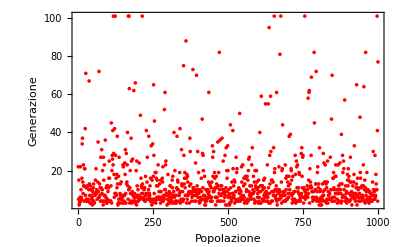

```mathematica
ListPlot[prove,Frame->True,FrameLabel->{"Popolazione","Generazione"},PlotStyle->{Red,PointSize[0.0065]},PlotRange->Full]
```

```mathematica
N[7077/500]
```

14.154

# CONTROLLO DEL RISULTATO SU UN DATO INIZIALE DIVERSO

```mathematica
(*PER VERIFICARE CHE LA SOLUZIONE TROVATA NON RISOLVA SOLO ED ESCLUSIVAMENTE PARTICOLARE CONDIZIONE INIZIALE, LA APPLICO AD ALTRE SITUAZIONI DI PARTENZA*)
uniR=RandomSample[uni];
taglio=RandomInteger[{0,9}];
cut=taglio;
stack0=Take[uniR,cut];
table0=Take[uniR,-(9-cut)];

stack=stack0;
Print["Stack iniziale: ",stack]
table=table0;
Print["Table iniziale: ",table]
Print["La soluzione del problema è: ",Soluzione]
Soluzione/.subs;
stack;
Print["Stack finale: ",stack]
table;
Print["Table finale: ",table]

If[stack===uni,
Print["Il programma risolve anche un'altra condizione iniziale"],
Print["Il programma NON risolve un'altra condizione iniziale"]
]
```

Stack iniziale: {v,a,r,i,l,n}

Table iniziale: {e,s,u}

La soluzione del problema è: xDU[xMS[xNN],xEQ[xEQ[xMT[xCS],xMS[xMS[xNN]]],xNOT[xMS[xMS[xNN]]]]]

Stack finale: {u,n,i,v,e,r,s,a,l}

Table finale: {}

Il programma risolve anche un'altra condizione iniziale